```mathematica
ClearAll["Global`*"]
```

```mathematica
(*GOES Proton flux comparitor*)
dA=(4088*4088)*(10*10^-4)^2; (*10 microns by 10 microns in cm^2 by the num of pix squared *)
dΩ=2*Pi; (* 2pi steradians*)
dt=3.04; (* exposure time between clock reset*)


(* Expected rate from Kruk, Hirata, et al 2016 *)
KHrate = 5.5;
KHavgFlux = KHrate * dA * dt;

GOESconverter[frac_]:= frac*dA*dΩ*dt

Print["The expected flux at L2 is ",KHavgFlux]
```

The expected flux at L2 is 279.42

```mathematica
(* Compare to values at https://www.swpc.noaa.gov/products/goes-proton-fluxhttps://www.swpc.noaa.gov/products/goes-proton-fluxNonehttps://www.swpc.noaa.gov/products/goes-proton-fluxHyperlinkActionRecycledHyperlinkActive *)
GOESconverter[.2]
```

63.8418

{time_tag,satellite,flux,energy}

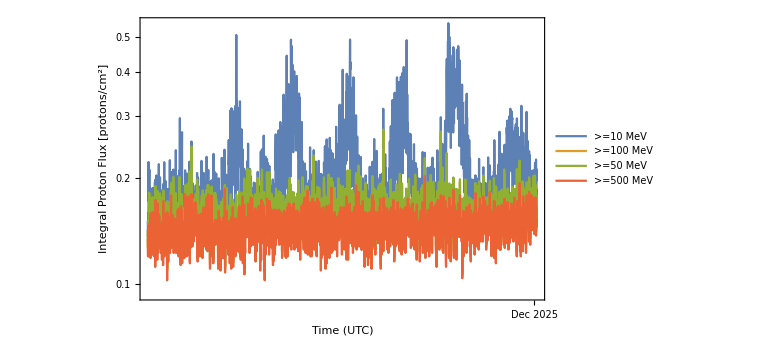

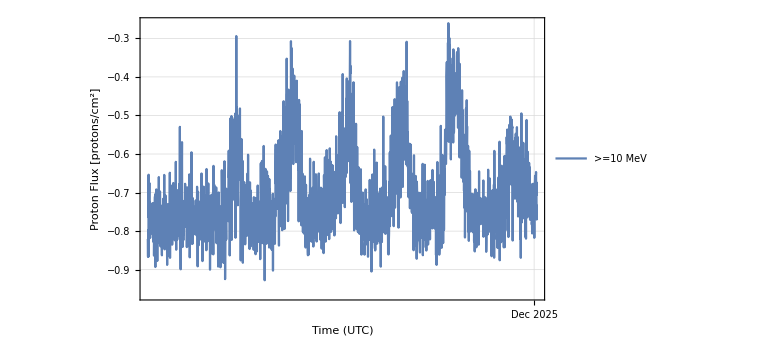

```mathematica
(* URL of the GOES integral proton JSON (1-day, plot version) *)
url = "https://services.swpc.noaa.gov/json/goes/primary/integral-protons-plot-7-day.json";

(* 1. Import JSON as a list of Associations *)
data = Import[url, "RawJSON"];

(* Optional: Inspect the keys available in one record *)
Keys[data[[1]]]

(* Most SWPC GOES time series have fields like:
   "time_tag"  -> ISO time string (UTC)
   "flux"      -> proton flux (protons / (cm^2 s sr)) for a given channel :contentReference[oaicite:0]{index=0}
   "energy"    -> energy threshold label, e.g. \">=10 MeV\"
*)

(* 2. Convert to a cleaner structure with DateObjects *)
processed =
  data /. a_Association :> <|
     "time"   -> DateObject[a["time_tag"]],
     "flux"   -> a["flux"],
     "energy" -> Lookup[a, "energy", "unknown"]
   |>;

(* 3. Group by energy channel (e.g. >=1 MeV, >=5 MeV, >=10 MeV, etc.) *)
byEnergy = GroupBy[processed, #["energy"] &];

(* 4. Build {time, flux} pairs for each energy channel *)
series =
  KeyValueMap[
    Function[{energyLabel, records},
      {
        energyLabel,
        records /. r_Association :> {r["time"], r["flux"]}
      }
    ],
    byEnergy
  ];

(* Extract just the data and legend labels *)
seriesData   = series[[All, 2]]; 
seriesLabels = series[[All, 1]];

(* 5. Plot flux vs time for all energy channels *)
DateListPlot[
  seriesData,
  Frame -> True,
  FrameLabel -> {"Time (UTC)", "Integral Proton Flux [protons/cm^2]"},
  PlotRange -> All,
  PlotLegends -> Placed[seriesLabels, {0.85, 0.5}],
  GridLines -> Automatic,
  ImageSize -> Large,
  ScalingFunctions -> {"Linear", "Log10"}  (* comment this line out if you don’t want log-flux *)
]


energyOfInterest = ">=10 MeV";  (* adjust to match the exact string in the JSON *)

subset = Select[processed, #["energy"] == energyOfInterest &];

singleSeries = subset /. r_Association :> {r["time"], r["flux"]};

DateListPlot[
  singleSeries,
  Frame -> True,
  FrameLabel -> {"Time (UTC)", "Proton Flux [protons/cm^2]"},
  PlotRange -> All,
  PlotLegends -> {energyOfInterest},
  GridLines -> Automatic,
  ImageSize -> Large,
  ScalingFunctions -> {"Linear", "Log10"}
]
```

```mathematica
convertedData = {};
For[i=1,i<Length[singleSeries],i++,
	AppendTo[convertedData,{singleSeries[[i,1]],GOESconverter[singleSeries[[i,2]]]}]
	]
```

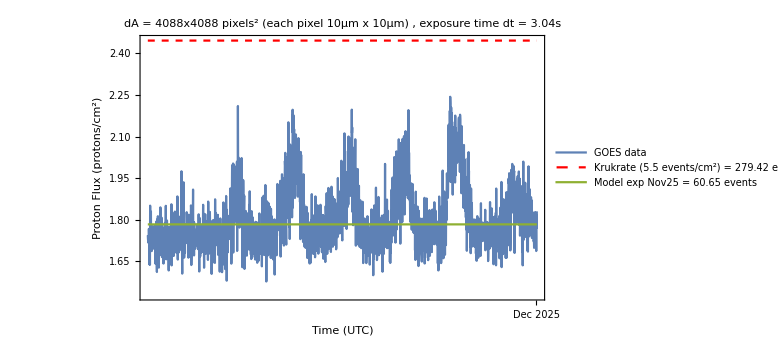

```mathematica
(* convertedData is {{time1, flux1}, {time2, flux2}, ...} *)
endOfNovModel = (forecastSeries[[-51,2]]+forecastSeries[[-50,2]])/2 ;

thresholdSeries = { #[[1]], KHavgFlux } & /@ convertedData;
modelSeries = { #[[1]], endOfNovModel } & /@ convertedData;

DateListPlot[
  {convertedData, thresholdSeries,modelSeries},
  PlotLabel->"dA = 4088x4088 pixels^2 (each pixel 10μm x 10μm) , exposure time dt = 3.04s",
  Frame -> True,
  FrameLabel -> {
    "Time (UTC)",
    "Proton Flux (protons/cm^2)"
  },
  PlotRange -> All,
  PlotStyle -> {
    Automatic,                             (* your original series style *)
    Directive[Red, Dashed, Thick]          (* horizontal line style *)
  },
  PlotLegends -> {"GOES data", StringForm["Krukrate (5.5 events/cm^2) = `` events",KHavgFlux],StringForm["Model exp Nov25 = `` events",endOfNovModel]},
  ImageSize -> Large,
  ScalingFunctions -> {"Linear", "Log10"}
]
```

```mathematica
forecastFile = "C:\\Users\\Owner\\Documents\\Hirata Group\\Code\\python\\Outputs\\ion forecast 2010 to 2030_10 instances.h5";
(* List the elements available in the HDF5 file *)
Import[forecastFile, "Elements"];

(* Specifically list datasets *)
Import[forecastFile, "Datasets"];

allParticles = Import[forecastFile, {"Datasets", "all_particles"}];
avgParticles = Import[forecastFile, {"Datasets", "avg_particles"}];
stdParticles = Import[forecastFile, {"Datasets", "std_particles"}];
datesRaw    = Import[forecastFile, {"Datasets", "dates"}];
correctedDates = Flatten[datesRaw][[;; ;;2]];

decimalYearToDate[dec_] := Module[
  {y = Floor[dec], f = FractionalPart[dec]},
  DatePlus[
    DateObject[{y, 1, 1}, TimeZone -> 0],
    {365.25 f, "Day"}
  ]
]

comparableDates = Map[decimalYearToDate,correctedDates];
```

```mathematica
forecastSeries = Transpose[{comparableDates, avgParticles}];

Manipulate[
  DateListPlot[
    forecastSeries,
    PlotRange -> {{tmin, tmax}, All},
    Frame -> True,
    ScalingFunctions -> {"Linear", "Log10"}
  ],
  {{tmin, First@comparableDates}, comparableDates},
  {{tmax, Last@comparableDates}, comparableDates}
]
```

```mathematica
forecastSeries[[-51]]
```

{Sun 16 Nov 2025,60.4}

Bandgap calculations

Casselman vs Chu equation for E_g , Chu is the closest to measured values(confirm with Chris who actually measured the bandgap)

```mathematica
energyGapCass[x_,T_]:= 1.92*x + 5.35*(10^-4)*T*(1-2*x) - 0.810*x^2 + 0.832*x^3 - 0.302

energyGapChu[x_,T_]:= 1.87x − 0.28 x^2  +  (6 − 14x + 3 x^2)*(10^-4)*T + 0.35 x^4 − 0.295
```

```mathematica
h = 6.582119569*10^-16 (* in eV/s *)
c = 2.99792458*10^8 (* in m/s *)
q = 0.30282212088 (* in C *)
Subscript[k, B] = 8.617333262×10^-5 (*(eV⋅K)^-1 *)
```

6.58212×10^-16

2.99792×10^8

0.302822

0.0000861733

```mathematica
energyGapCutoff[λ_]:= 1240 / (λ*10^9)  (* Using hc ~ 1240 eV*nm *)
tempToEnergy[T_]:= Subscript[k, B]*T
```

```mathematica
Print["Casselman E_g = ", energyGapCass[0.445,89] ," eV"]
Print["Chu E_g = ", energyGapChu[0.445,89] ," eV"]
Print["E_g based on the wavelength of the photon is = ", energyGapCutoff[2.5*10^-6]," eV"]
Print["The diff btwn Chu and photon E_g is = ", (energyGapChu[0.445,95]-energyGapCutoff[2.5*10^-6])*1000," meV"]
```

Casselman E_g = 0.470554 eV

Chu E_g = 0.498668 eV

E_g based on the wavelength of the photon is = 0.496 eV

The diff btwn Chu and photon E_g is = 2.88658 meV

```mathematica
Print["An environment at 89 Kelvin has a Boltzmann energy of ",tempToEnergy[89]*1000 ," meV"]
Print["That energy is ", (energyGapChu[0.445,89]/tempToEnergy[89]), " times smaller than the band gap energy,"]
Print[" or ", (tempToEnergy[89]/energyGapChu[0.445,89])*100, "% of the band gap energy"]
```

An environment at 89 Kelvin has a Boltzmann energy of 7.66943 meV

That energy is 65.0203 times smaller than the band gap energy,

or 1.53798% of the band gap energy

```mathematica
wavelengthToE[γ_]:= 1.2398/γ//N (* this is in units of eV/μm *)

Print["A .48 micron wavelength photon has ",energy1=wavelengthToE[.48]," eVs of energy"]
Print["A 2.5 micron wavelength photon has ",energy2=wavelengthToE[2.5]," eVs of energy"]


Print["Our detectors cover an energy range from ",energy2," eV to ",energy1, " eV"]
```

A .48 micron wavelength photon has 2.58292 eVs of energy

A 2.5 micron wavelength photon has 0.49592 eVs of energy

Our detectors cover an energy range from 0.49592 eV to 2.58292 eV

Secondary delta electron flux calculations

```mathematica
1/Log[λ[E]]* Sum[z^2*β^2*Sum[(Subscript[F, z][Subscript[E, z]])/Subscript[β, z]^2(1/2*(1/E - 1/(Subscript[W, max][Subscript[E, z]])) - Subscript[β, z]^2/(Subscript[W, max][Subscript[E, z]])*Log[(Subscript[W, max][Subscript[E, z]])/E ,{Subscript[E, z,min],Infinity}],{-1,92}]
```

Scratch calculations

(√(e (e+2 m)))/(e+m)

```mathematica
(1/(e+m))*Sqrt[e(e+2*m)]//FullSimplify
```

```mathematica
D[Sqrt[e(e+2*m)],e]//FullSimplify
```

(e+m)/(√(e (e+2 m)))

```mathematica
(e+m)^2-m^2//FullSimplify
```

e (e+2 m)

```mathematica
beta=(1/(e + m))*Sqrt[(e + m)^2-m^2]//FullSimplify
```

(√(e (e+2 m)))/(e+m)

```mathematica
(e+m)/m
```

(e+m)/m

```mathematica
denom=Sqrt[1-beta^2]//FullSimplify
gamma=1/denom//FullSimplify
```

√(m^2/(e+m)^2)

1/(√(m^2/(e+m)^2))

```mathematica
phi[r_,c_,b_,a_,g_,d_,f_]:= ((c*b^a)*(1/r^g))*(r*(1/(r+ f)))^d
phi[R,ℭ,β,α,γ,Δ,ℜ]
```

R^-γ ℭ (R/(R+ℜ))^Δ β^α

```mathematica
D[phi[R,ℭ,β,α,γ,Δ,ℜ], R]
dr=FullSimplify[D[phi[R,ℭ,β,α,γ,Δ,ℜ], R]]
```

-R^(-1-γ) ℭ (R/(R+ℜ))^Δ β^α γ+R^-γ ℭ (R/(R+ℜ))^(-1+Δ) (-R/(R+ℜ)^2+1/(R+ℜ)) β^α Δ

-R^(-2-γ) ℭ (R/(R+ℜ))^(1+Δ) β^α ((R+ℜ) γ-ℜ Δ)

```mathematica
FullSimplify[dr/phi[R,ℭ,β,α,γ,Δ,ℜ]]
FullSimplify[dr/phi[R,ℭ,β,α,γ,Δ,ℜ]]*R
```

(-γ+(ℜ Δ)/(R+ℜ))/R

-γ+(ℜ Δ)/(R+ℜ)

```mathematica
FullSimplify[D[Sqrt[(e*(e+2m))],e]]
```

(e+m)/(√(e (e+2 m)))

```mathematica
h = Entity["PhysicalConstant", "PlanckConstant"]["Value"]
c = Entity["PhysicalConstant", "SpeedOfLight"]["Value"]
```

132521403/200000000000000000000000000000000000000000 s J

299792458 m/s

```mathematica
reducedPlanck=6.582119569 * (10)^-16 (*eV/s*)
massE=0.51099895069*(10^6) (*eV/c^2*)
```

6.58212×10^-16

510999.

```mathematica
sol1=Solve[k^2*reducedPlanck^2*(1/(2*massE*c^2))==energy1,k]
sol2=Solve[k^2*reducedPlanck^2*(1/(2*massE*c^2))==energy2,k]
```

{{k→-7.40006×10^26 m/s},{k→7.40006×10^26 m/s}}

{{k→-3.38058×10^26 m/s},{k→3.38058×10^26 m/s}}

```mathematica
val1=sol1[[2,1,2]]/(2*Pi)
val2=sol2[[2,1,2]]/(2*Pi)

Print[1/val1]
```

1.17776×10^26 m/s

5.38037×10^25 m/s

8.49072×10^-27 s/m